```mathematica
V[ϕ_]:= M^4(1 - (ϕ/μ)^p)
```

```mathematica
1/2(D[V[ϕ],ϕ]/V[ϕ])^2/.{p->4}//FullSimplify
```

```mathematica
Solve[(8 ϕ^6)/((μ^4-ϕ^4)^2)==1, ϕ]//FullSimplify
```

$Aborted

```mathematica
ϵ20 [ϕ_]:=ϕ^6/(3200000000 (1-ϕ^4/160000)^2)
```

```mathematica
ϵ1[ϕ_]:=(8 ϕ^6)/((1-ϕ^4)^2)
```

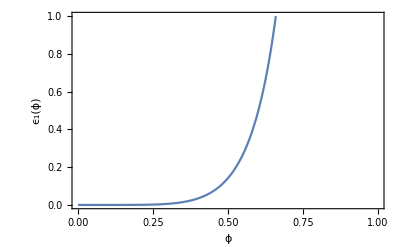

```mathematica
Plot[{ϵ1[ϕ]}//Evaluate,{ϕ,0,1},Frame->True,FrameLabel->{"ϕ", "ϵ_1(ϕ)"},PlotRange->{0,1}]
```

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}}, endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-50==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
Parallelize[Table[{μ , cend[4,μ][[1]], cini[4,μ][[1]]},{μ,1,100,5}]]
```

CompiledFunction::cfse: Compiled expression {0.659399} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {30.3164} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {40.3108} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {50.3073} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {55.3061} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {10.3556} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {20.3271} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {45.3089} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {0.659399} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {30.3164} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {40.3108} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {50.3073} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {55.3061} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {10.3556} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {20.3271} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {45.3089} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {0.0498301} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {22.5565} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {32.1835} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {41.9515} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {46.8658} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {4.85886} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {13.2461} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {37.0553} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression {51.7938} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {56.7325} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {61.6797} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {81.5259} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {86.4974} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {66.6338} should be a machine-size real number.

CompiledFunction::cfse: Compiled expression {71.5934} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {76.5577} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

```mathematica
{{1,0.659399152881071,0.04983010772273638},{6,5.4003635322549215,1.6590567860808276},{11,10.35558017238564,4.858859554819006},{16,15.337120009797683,8.85720730175267},{21,20.32705456781059,13.246093084313767},{26,25.320719979284032,17.841614816713122},{31,30.316366678863847,22.556461613756536},{36,35.31319098252798,27.345501235392597},{41,40.310772051522754,32.183489585571486},{46,45.308868208174566,37.055340551445454},{51,50.30733077360558,41.95153386550125},{56,55.30606326359508,46.86578549525636},{61,60.30500033385517,51.7937893428139},{66,65.30409615578643,56.73250017722858},{71,70.30331763732008,61.67970584935916},{76,75.30264028592616,66.63376184407375},{81,80.30204558570085,71.59342086111555},{86,85.30151927923444,76.55772010878549},{91,90.3010502099419,81.52590479726112},{96,95.30062952256385,86.49737499362054}}//TableForm
```

1 | 0.659399 | 0.0498301
6 | 5.40036 | 1.65906
11 | 10.3556 | 4.85886
16 | 15.3371 | 8.85721
21 | 20.3271 | 13.2461
26 | 25.3207 | 17.8416
31 | 30.3164 | 22.5565
36 | 35.3132 | 27.3455
41 | 40.3108 | 32.1835
46 | 45.3089 | 37.0553
51 | 50.3073 | 41.9515
56 | 55.3061 | 46.8658
61 | 60.305 | 51.7938
66 | 65.3041 | 56.7325
71 | 70.3033 | 61.6797
76 | 75.3026 | 66.6338
81 | 80.302 | 71.5934
86 | 85.3015 | 76.5577
91 | 90.3011 | 81.5259
96 | 95.3006 | 86.4974

```mathematica
{{1,0.659399152881071,0.045514175860860345},{6,5.4003635322549215,1.5333018469110486},{11,10.35558017238564,4.563803387444165},{16,15.337120009797683,8.427177619183134},{21,20.32705456781059,12.719525138529415},{26,25.320719979284032,17.245809341518218},{31,30.316366678863847,21.909587167783393},{36,35.31319098252798,26.65978478165869},{41,40.310772051522754,31.46739926842118},{46,45.308868208174566,36.31492457379894},{51,50.30733077360558,41.191237083344866},{56,55.30606326359508,46.08895818292538},{61,60.30500033385517,51.003013259150045},{66,65.30409615578643,55.92980364584774},{71,70.30331763732008,60.866709533233674},{76,75.30264028592616,65.81178003070286},{81,80.30204558570085,70.76353343375698},{86,85.30151927923444,75.7208247321802},{91,90.3010502099419,80.68275545216092},{96,95.30062952256385,85.64861090216783}}//TableForm
```

1 | 0.659399 | 0.0455142
6 | 5.40036 | 1.5333
11 | 10.3556 | 4.5638
16 | 15.3371 | 8.42718
21 | 20.3271 | 12.7195
26 | 25.3207 | 17.2458
31 | 30.3164 | 21.9096
36 | 35.3132 | 26.6598
41 | 40.3108 | 31.4674
46 | 45.3089 | 36.3149
51 | 50.3073 | 41.1912
56 | 55.3061 | 46.089
61 | 60.305 | 51.003
66 | 65.3041 | 55.9298
71 | 70.3033 | 60.8667
76 | 75.3026 | 65.8118
81 | 80.302 | 70.7635
86 | 85.3015 | 75.7208
91 | 90.3011 | 80.6828
96 | 95.3006 | 85.6486

## Plots SR

```mathematica
k0002n60  = {{1,0.9418793835059156+0.*I,1.8986509462236458*^-6+0.*I},
{2,0.9441561995712241+0.*I,0.00002689028333954933+0.*I},
{3,0.9461098722369713+0.*I,0.0001218277311949866+0.*I},
{4,0.9480646003630375+0.*I,0.00034226089635447783+0.*I},
{5,0.9500166979192515+0.*I,0.0007355090809388987+0.*I},
{6,0.9519617881755984+0.*I,0.0013301091079367276+0.*I},
{7,0.9538161652033381+0.*I,0.0021329565408752106+0.*I},
{8,0.9555724963149217+0.*I,0.003132266445449954+0.*I},
{9,0.9571976671275582+0.*I,0.00430334389100008+0.*I},
{10,0.9586827591108323,0.005614654433068296},
{11,0.9600345070570707,0.007032783702080216},
{12,0.9612430892601784,0.008525833850179873},
{13,0.96232596194969,0.010065368665971675},
{14,0.9632981450445992,0.011627271261117676},
{15,0.964165731144023,0.01319186357141902},
{16,0.9649360408810884,0.014743616117106357},
{17,0.9656267948926345,0.01627064478656332},
{18,0.9662410882957015,0.017764147878195354},
{19,0.9667934715589722,0.01921785187371547},
{20,0.9672887071909434,0.02062750999541509},
{21,0.9677336044617996,0.021990473396112018},
{22,0.9681318701801237,0.023305330838228253},
{23,0.968493042987042,0.024571614151357776},
{24,0.9688199378653657,0.025789561377395243},
{25,0.9691162432842108,0.02695993227093456},
{26,0.9693854300478758,0.028083860764645696},
{27,0.9696305267196759,0.029162741173880517},
{28,0.9698541787952836,0.030198140418500254},
{29,0.9700566242914017,0.031191730974771483},
{30,0.9702440720589285,0.03214523990119079},
{31,0.9704161947679065,0.033060411118125875},
{32,0.9705745564688707,0.03393897761693687},
{33,0.9707205346909484,0.03478264111514769},
{34,0.9708553458423362,0.035593057633349454},
{35,0.9709800662159929,0.03637182761294129},
{36,0.9710956490631364,0.03712048949544755},
{37,0.9712029417821227,0.03784051592265989},
{38,0.9713026987717273,0.038533311905450514},
{39,0.9713955925828313,0.039200214455627144},
{40,0.9714822241513937,0.03984249329037143},
{41,0.9715631321358386,0.04046135230831779},
{42,0.971638799421664,0.0410579316068557},
{43,0.9717096606012008,0.041633309863819266},
{44,0.9717747146921648,0.04218850694462644},
{45,0.9718371103587241,0.042724486615897894},
{46,0.9718957624342806,0.043242159371011946},
{47,0.9719509596175165,0.04374238523346688},
{48,0.9720029642091665,0.044225976502900465},
{49,0.9720520146377573,0.04469370042931481},
{50,0.9720983264780103,0.045146281794832224},
{51,0.9721420980107461,0.04558440538892378},
{52,0.9721835091477435,0.04600871837009606},
{53,0.9722227245569639,0.0464198325088681},
{54,0.9722598952288957,0.04681832631128746},
{55,0.9722951588678379,0.04720474702408919},
{56,0.9723286426962419,0.04757961252336187},
{57,0.9723604630273636,0.04794341309115022},
{58,0.9723907274524156,0.04829661308360055},
{59,0.972419535108667,0.0486396524960451},
{60,0.9724469768090942,0.04897294842992987},
{61,0.9724731366454743,0.04929689646662596},
{62,0.9724980929732007,0.04961187195364036},
{63,0.9725219177676662,0.049918231208457495},
{64,0.9725446779273353,0.050216312644698724},
{65,0.9725664357116431,0.05050643782569248},
{66,0.9725872484909026,0.05078891245015612},
{67,0.9726071698116528,0.05106402727410469},
{68,0.9726262495882975,0.051332058973512194},
{69,0.9726445342331973,0.05159327095148028},
{70,0.9726620671429493,0.0518479140935922},
{71,0.9726788888138584,0.05209622747520487},
{72,0.9726950369824324,0.05233843902358153},
{73,0.9727105466914867,0.05257476613817819},
{74,0.9727254511513412,0.05280541627179947},
{75,0.97273978129081,0.05303058747533703},
{76,0.9727535663224166,0.05325046890856131},
{77,0.9727668328494622,0.053465241319365545},
{78,0.9727796074350052,0.05367507749314141},
{79,0.9727919131328736,0.053880142675204565},
{80,0.9728037732025318,0.05408059496688993},
{81,0.972815207614207,0.054276585698332894},
{82,0.9728262375683425,0.054468259778300415},
{83,0.9728368818687818,0.05465575602372535},
{84,0.972847157225763,0.05483920746935989},
{85,0.9728570818210812,0.055018741659292256},
{86,0.9728666701471131,0.05519448092168387},
{87,0.9728759383787078,0.05536654262723201},
{88,0.9728848990686211,0.055535039433172936},
{89,0.9728935666095628,0.055700079512987034},
{90,0.972901953693959,0.05586176677333314},
{91,0.9729100724417128,0.05602020105868844},
{92,0.9729179333608297,0.05617547834464386},
{93,0.9729255473971495,0.05632769092033432},
{94,0.9729329257443816,0.05647692756101474},
{95,0.972940076373209,0.05662327369110267},
{96,0.9729461289282656,0.056766811538382055},
{97,0.9729528553173878,0.05690762027945697},
{98,0.9729593817150397,0.05704577617861761},
{99,0.9729657149631392,0.05718135271868091},
{100,0.97297186245833,0.05731442072483846}};

k0002n50 = {{1,0.9285077310531795+0.*I,3.571137540130252*^-6+0.*I},
{2,0.931889106094342+0.*I,0.000049244751289298464+0.*I},
{3,0.934727296674888+0.*I,0.00021804202606157867+0.*I},
{4,0.9375062507098578+0.*I,0.0005987419653655496+0.*I},
{5,0.9402341742831807+0.*I,0.0012574762343258022+0.*I},
{6,0.9428403781749868+0.*I,0.0022230252641167033+0.*I},
{7,0.9452995445361477+0.*I,0.003487458193105628+0.*I},
{8,0.9475380376231075+0.*I,0.00501585451808053+0.*I},
{9,0.9495933146279226+0.*I,0.006758416363639573+0.*I},
{10,0.9514167232151316+0.*I,0.00866079287294907+0.*I},
{11,0.953036348034833+0.*I,0.010671093719262465+0.*I},
{12,0.9544779834745726+0.*I,0.01274374867626851+0.*I},
{13,0.9557417903933362+0.*I,0.014841025780048872+0.*I},
{14,0.9568556073011428+0.*I,0.016933069090581905+0.*I},
{15,0.9578428744493463+0.*I,0.018997168151238086+0.*I},
{16,0.9587139592115232+0.*I,0.02101668793335622+0.*I},
{17,0.9594787957355175+0.*I,0.022979956935290598+0.*I},
{18,0.9601603043710275+0.*I,0.024879228384046298+0.*I},
{19,0.9607661057900267+0.*I,0.026709785472855463+0.*I},
{20,0.9613055051361906+0.*I,0.028469210631258655+0.*I},
{21,0.9617822679728796+0.*I,0.03015679188827352+0.*I},
{22,0.9622135396101898+0.*I,0.0317730571114472+0.*I},
{23,0.962600757813519+0.*I,0.03331941420743746+0.*I},
{24,0.9629493831376447+0.*I,0.03479787917052051+0.*I},
{25,0.9632641137791719+0.*I,0.03621086916899265+0.*I},
{26,0.963548997816707+0.*I,0.03756104779112895+0.*I},
{27,0.9638075301295507+0.*I,0.03885121069066163+0.*I},
{28,0.9640427334526444+0.*I,0.04008420212057213+0.*I},
{29,0.9642538747921963+0.*I,0.04126285491259517+0.*I},
{30,0.9644499893052703+0.*I,0.0423899478999233+0.*I},
{31,0.9646296591717609+0.*I,0.04346817700720144+0.*I},
{32,0.9647946186443254+0.*I,0.04450013647550359+0.*I},
{33,0.9649463869462703+0.*I,0.045488307089059925+0.*I},
{34,0.9650862978063843+0.*I,0.0464350497961197+0.*I},
{35,0.9652155252918071+0.*I,0.047342603258203726+0.*I},
{36,0.9653351054168664+0.*I,0.048213084216689586+0.*I},
{37,0.965445954669936+0.*I,0.04904848984187527+0.*I},
{38,0.9655488859809662+0.*I,0.04985070143963238+0.*I},
{39,0.9656446213352172+0.*I,0.05062148905058471+0.*I},
{40,0.9657338043886509+0.*I,0.051362516597102094+0.*I},
{41,0.9658170096637515+0.*I,0.05207534732534837+0.*I},
{42,0.9658947511242819+0.*I,0.05276144935840298+0.*I},
{43,0.9659674897823888+0.*I,0.05342220122863713+0.*I},
{44,0.9660356393901106+0.*I,0.05405889729641718+0.*I},
{45,0.9660995731190435+0.*I,0.05467275299213218+0.*I},
{46,0.9661596271694018+0.*I,0.055264909839658094+0.*I},
{47,0.966213894791167+0.*I,0.0558364402328485+0.*I},
{48,0.9662670872183406+0.*I,0.05638835193614669+0.*I},
{49,0.9663172280400069+0.*I,0.05692159236839934+0.*I},
{50,0.9663645435633333+0.*I,0.0574370526123232+0.*I},
{51,0.9664092396532673+0.*I,0.05793557115865949+0.*I},
{52,0.9664515050024649+0.*I,0.058417937404425704+0.*I},
{53,0.9664915106678678+0.*I,0.058884894916725286+0.*I},
{54,0.9665294136277476+0.*I,0.05933714447335073+0.*I},
{55,0.9665653575728791+0.*I,0.05977534689283395+0.*I},
{56,0.9665994743099267+0.*I,0.06020012566643119+0.*I},
{57,0.9666318842553867+0.*I,0.06061206940509574+0.*I},
{58,0.9666626988689258+0.*I,0.06101173411293955+0.*I},
{59,0.9666920204160724+0.*I,0.06139964529986285+0.*I},
{60,0.9667199431829838+0.*I,0.06177629994409304+0.*I},
{61,0.966746554169865+0.*I,0.062142168315552394+0.*I},
{62,0.9667719339693956+0.*I,0.06249769566995861+0.*I},
{63,0.9667961566560324+0.*I,0.06284330382351526+0.*I},
{64,0.9668192914281881+0.*I,0.06317939261637397+0.*I},
{65,0.9668414017168484+0.*I,0.06350634127385371+0.*I},
{66,0.9668625473995364+0.*I,0.06382450967224014+0.*I},
{67,0.9668827832964477+0.*I,0.06413423951717594+0.*I},
{68,0.9669021605273378+0.*I,0.0644358554403299+0.*I},
{69,0.9669207270993768+0.*I,0.0647296660208885+0.*I},
{70,0.9669385270673843+0.*I,0.06501596473761131+0.*I},
{71,0.9669556020691178+0.*I,0.06529503085605722+0.*I},
{72,0.9669719905106293+0.*I,0.06556713025647591+0.*I},
{73,0.9669877291616098+0.*I,0.06583251620604429+0.*I},
{74,0.967002851678469+0.*I,0.0660914300803695+0.*I},
{75,0.9670173894471286+0.*I,0.06634410203716548+0.*I},
{76,0.9670313721438312+0.*I,0.06659075164603384+0.*I},
{77,0.9670448277448108+0.*I,0.06683158847736292+0.*I},
{78,0.9670577822682902+0.*I,0.06706681265368657+0.*I},
{79,0.9670702604262744+0.*I,0.06729661536542035+0.*I},
{80,0.9670822850757111+0.*I,0.06752117935444107+0.*I},
{81,0.9670938778436171+0.*I,0.06774067936688039+0.*I},
{82,0.9671050594038268+0.*I,0.06795528257802827+0.*I},
{83,0.9671158482566251+0.*I,0.06816514899102104+0.*I},
{84,0.9671262633147596+0.*I,0.06837043181078357+0.*I},
{85,0.9671363211138324+0.*I,0.06857127779571058+0.*I},
{86,0.9671460386407895+0.*I,0.06876782758775224+0.*I},
{87,0.9671554296585314+0.*I,0.06896021602327622+0.*I},
{88,0.9671645099730836+0.*I,0.06914857242480699+0.*I},
{89,0.9671732924606077+0.*I,0.06933302087636042+0.*I},
{90,0.9671817900520902+0.*I,0.06951368048223795+0.*I},
{91,0.9671900145177869+0.*I,0.06969066561113503+0.*I},
{92,0.9671979786473446+0.*I,0.06986408612590703+0.*I},
{93,0.9672056921857061+0.*I,0.07003404760088631+0.*I},
{94,0.9672131658547392+0.*I,0.07020065152621499+0.*I},
{95,0.9672204092664679+0.*I,0.07036399550130126+0.*I},
{96,0.9672274319619665+0.*I,0.07052417341732854+0.*I},
{97,0.9672342430353476+0.*I,0.07068127562962752+0.*I},
{98,0.9672408513694247+0.*I,0.07083538912071652+0.*I},
{99,0.9672472639058485+0.*I,0.07098659765498669+0.*I},
{100,0.9672534886815499+0.*I,0.07113498192390773+0.*I}};
```

```mathematica
muns0002n60 =Table[{μ, k0002n60[[μ,2]]},{μ,Length[k0002n60]}];
mur0002n60 = Table[{μ, k0002n60[[μ,3]]},{μ,Length[k0002n60]}];
muns0002n50 = Table[{μ, k0002n50[[μ,2]]},{μ,Length[k0002n50]}];
mur0002n50 = Table[{μ, k0002n50[[μ,3]]},{μ,Length[k0002n50]}];
nsr0002n50 = Table[{k0002n50[[μ,2]], k0002n50[[μ,3]]},{μ,Length[k0002n50]}];
nsr0002n60= Table[{k0002n60[[μ,2]], k0002n60[[μ,3]]},{μ,Length[k0002n60]}];
```

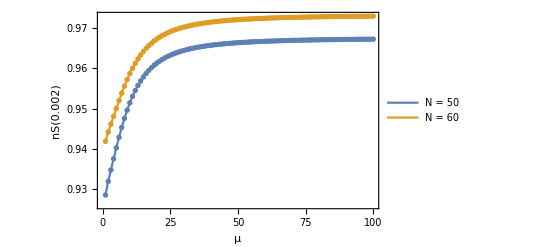

```mathematica
plot1 = ListPlot[{muns0002n50,muns0002n60},Joined->True,PlotRange->All,Mesh->Full,PlotLegends->Placed[{"N = 50","N = 60"},{Scaled[{0.5,0.3}], {0, 0.5}}],Frame->True,FrameLabel->{"μ","nS(0.002)"}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Presentation_plots\\mu_vs_ns0002.png",plot1]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Presentation_plots\mu_vs_ns0002.png

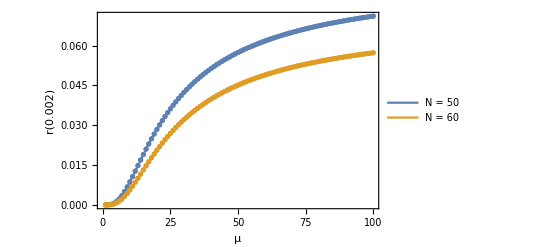

```mathematica
plot2 = ListPlot[{mur0002n50,mur0002n60},Joined->True,PlotRange->All,Mesh->Full,PlotLegends->Placed[{"N = 50","N = 60"},{Scaled[{0.5,0.3}], {0, 0.5}}],Frame->True,FrameLabel->{"μ","r(0.002)"}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Presentation_plots\\mu_vs_r0002.png",plot2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Presentation_plots\mu_vs_r0002.png

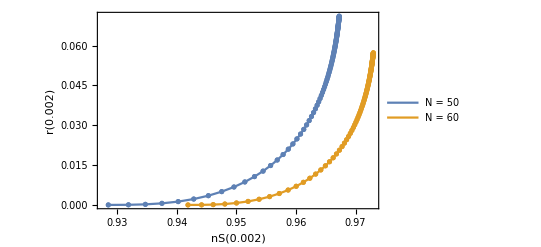

```mathematica
plot3 = ListPlot[{nsr0002n50,nsr0002n60},Joined->True,PlotRange->All,Mesh->Full,PlotLegends->Placed[{"N = 50","N = 60"},{Scaled[{0.2,0.3}], {0, 0.5}}],Frame->True,FrameLabel->{"nS(0.002)","r(0.002)"}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Presentation_plots\\ns_vs_r0002.png",plot3]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Presentation_plots\ns_vs_r0002.png

```mathematica
k005n60 = {{1,0.9375567086533892,2.3618119097491904*^-6},
{2,0.9405970141801048+0.*I,0.000032453818380006465+0.*I},
{3,0.9427972158972185+0.*I,0.00014601784405096125+0.*I},
{4,0.9449838473951667+0.*I,0.0004073905986049268+0.*I},
{5,0.9471497737120299+0.*I,0.0008693667777503604+0.*I},
{6,0.9492924177395798+0.*I,0.001561289787962636+0.*I},
{7,0.951317523344677+0.*I,0.002486819417809358+0.*I},
{8,0.9532216885363614+0.*I,0.0036284750901997825+0.*I},
{9,0.954970868418752+0.*I,0.004955034375523379+0.*I},
{10,0.9565586232215205+0.*I,0.0064287844959352546+0.*I},
{11,0.95799569515673+0.*I,0.008011124435917751+0.*I},
{12,0.9592728658008868+0.*I,0.009666178407759704+0.*I},
{13,0.9604116199293071+0.*I,0.011362689716658103+0.*I},
{14,0.961431428247229+0.*I,0.01307470417422952+0.*I},
{15,0.9623322537655702+0.*I,0.014781479166488738+0.*I},
{16,0.963136923751589+0.*I,0.016466987251206936+0.*I},
{17,0.9638493188779771+0.*I,0.018119250392127372+0.*I},
{18,0.9644873211770056+0.*I,0.01972964028029624+0.*I},
{19,0.965056862978064+0.*I,0.021292224517181272+0.*I},
{20,0.9655663479400279+0.*I,0.022803199200066935+0.*I},
{21,0.9660203692465924+0.*I,0.024260406779965875+0.*I},
{22,0.9664309298295275+0.*I,0.02566294104984208+0.*I},
{23,0.9667998307894704+0.*I,0.027010835092604414+0.*I},
{24,0.9671338743071402+0.*I,0.028304808510177373+0.*I},
{25,0.9674362644152947+0.*I,0.029546075414890835+0.*I},
{26,0.9677106543258287+0.*I,0.03073619321526916+0.*I},
{27,0.9679602203605052+0.*I,0.03187694722023613+0.*I},
{28,0.9681877282111057+0.*I,0.03297026306949+0.*I},
{29,0.9683932291446339+0.*I,0.03401814092418499+0.*I},
{30,0.9685835865884+0.*I,0.03502260608547091+0.*I},
{31,0.9687582511766263+0.*I,0.0359856735145191+0.*I},
{32,0.968918841890136+0.*I,0.036909322429947405+0.*I},
{33,0.9690667821900055+0.*I,0.0377954779686595+0.*I},
{34,0.9692033265625337+0.*I,0.038645998858125405+0.*I},
{35,0.9693295831470256+0.*I,0.03946266950471037+0.*I},
{36,0.9694465320970457+0.*I,0.0402471953981083+0.*I},
{37,0.9695550439170342+0.*I,0.041001200983137545+0.*I},
{38,0.9696558916077543+0.*I,0.041726229348451306+0.*I},
{39,0.9697497643558851+0.*I,0.04242374323167629+0.*I},
{40,0.9698372773737081+0.*I,0.04309512696033888+0.*I},
{41,0.9699189810271565+0.*I,0.04374168903796871+0.*I},
{42,0.9699953684950602+0.*I,0.044364665155716014+0.*I},
{43,0.9700668826886454+0.*I,0.044965221463815916+0.*I},
{44,0.9701339226997803+0.*I,0.045544457979406115+0.*I},
{45,0.9701968483971547+0.*I,0.046103412039092476+0.*I},
{46,0.970254422282388+0.*I,0.046643061640932376+0.*I},
{47,0.9703100744219298+0.*I,0.047164328925347165+0.*I},
{48,0.9703624963788519+0.*I,0.04766808343664021+0.*I},
{49,0.970411930567996+0.*I,0.048155145222709354+0.*I},
{50,0.9704585964008514+0.*I,0.048626287825349876+0.*I},
{51,0.9705026948255244+0.*I,0.04908224112175228+0.*I},
{52,0.9705444082954434+0.*I,0.04952369401437849+0.*I},
{53,0.9705839038990108+0.*I,0.049951296969413805+0.*I},
{54,0.9706213344492542+0.*I,0.05036566440592263+0.*I},
{55,0.9706568401890112+0.*I,0.05076737694010096+0.*I},
{56,0.970690549515908+0.*I,0.05115698349004702+0.*I},
{57,0.9707225802494035+0.*I,0.05153500324704742+0.*I},
{58,0.970753041680837+0.*I,0.05190192751982038+0.*I},
{59,0.9707820330187791+0.*I,0.052258221459307246+0.*I},
{60,0.9708096470659514+0.*I,0.052604325669641135+0.*I},
{61,0.9708359688108466+0.*I,0.05294065771343741+0.*I},
{62,0.9708610774123393+0.*I,0.05326761351688959+0.*I},
{63,0.9708850451968045+0.*I,0.05358556868205863+0.*I},
{64,0.9709079402049867,0.05389487974392831},
{65,0.9709298251497668,0.05419588523910263},
{66,0.9709507579372375,0.05448890680133623},
{67,0.970970792895684,0.05477425019727708},
{68,0.9709899799816241,0.055052206233597405},
{69,0.971008366626105,0.05532305162677572},
{70,0.9710259962066983,0.055587049816304725},
{71,0.9710429097033814,0.055844451724572655},
{72,0.9710591449396831,0.05609549646769784},
{73,0.9710747375813317,0.05634041202038916},
{74,0.9710897211605696,0.05657941583821897},
{75,0.9711041265040271,0.05681271544036436},
{76,0.9711179834756681,0.057040508955160156},
{77,0.9711313188957804,0.05726298563171684},
{78,0.9711441585003557,0.05748032631922738},
{79,0.9711565273450553,0.05769270391665261},
{80,0.971168446658966,0.057900283794850065},
{81,0.9711799394275746,0.05810322419245145},
{82,0.9711910241861427,0.05830167658830151},
{83,0.9712017214472486,0.058495786050819946},
{84,0.971212047832837,0.05868569156691536},
{85,0.9712220208743194,0.058871526351035715},
{86,0.9712316554909886,0.0590534181363241},
{87,0.9712409688948385,0.059231489448241526},
{88,0.9712499733234329,0.059405857863010156},
{89,0.9712586822444341,0.05957663625049858},
{90,0.971267109671361,0.059743933003446756},
{91,0.9712752672475732,0.05990785225385247},
{92,0.9712831655760314,0.060068494077089044},
{93,0.9712908153604365,0.06022595468433942},
{94,0.9712982282104057,0.06038032660474274},
{95,0.9713054126853147,0.0605316988573563},
{96,0.9713123789699243,0.06068015711368069},
{97,0.9713191354709124,0.06082578385149287},
{98,0.971325689742471,0.06096865850030042},
{99,0.9713320502952919,0.0611088575790871},
{100,0.971338224996114,0.06124645482676756}};

k005n50 = {{1,0.922571757062828,4.557841350218423*^-6},{2,0.9265194175588753+0. ⅈ,0.00006208839338989208+0. ⅈ},{3,0.9297992340706632+0. ⅈ,0.0002720921425845828+0. ⅈ},{4,0.9329795867733414+0. ⅈ,0.0007396944624066558+0. ⅈ},{5,0.9360679822121669+0. ⅈ,0.0015381955044670695+0. ⅈ},{6,0.9389848885489384+0. ⅈ,0.002693341585432449+0. ⅈ},{7,0.9417095771393464+0. ⅈ,0.004187046451406558+0. ⅈ},{8,0.9441627803775986+0. ⅈ,0.005971282527915444+0. ⅈ},{9,0.9463978448723216+0. ⅈ,0.007983466618892847+0. ⅈ},{10,0.948362618650324,0.010158587980420318},{11,0.9500949630884015+0. ⅈ,0.012436809354460433+0. ⅈ},{12,0.9516215466447855+0. ⅈ,0.01476718716664107+0. ⅈ},{13,0.9529659088233469+0. ⅈ,0.017108728141766016+0. ⅈ},{14,0.954136282467064+0. ⅈ,0.01942990117877666+0. ⅈ},{15,0.9551701445650763+0. ⅈ,0.02170742712117228+0. ⅈ},{16,0.9560723262015611+0. ⅈ,0.02392483866311061+0. ⅈ},{17,0.9568727394967549+0. ⅈ,0.02607108267482907+0. ⅈ},{18,0.9575773987465652+0. ⅈ,0.02813928688143612+0. ⅈ},{19,0.9582035453591976+0. ⅈ,0.030125733933018928+0. ⅈ},{20,0.9587597205425878+0. ⅈ,0.03202904125068396+0. ⅈ},{21,0.9592552308408434+0. ⅈ,0.033849515905100845+0. ⅈ},{22,0.9596924727276306+0. ⅈ,0.03558865741584514+0. ⅈ},{23,0.9600894519250525+0. ⅈ,0.03724878000122363+0. ⅈ},{24,0.9604463191500293+0. ⅈ,0.03883273332230039+0. ⅈ},{25,0.9607680472535419+0. ⅈ,0.04034369461380624+0. ⅈ},{26,0.9610589041124291+0. ⅈ,0.04178501602305603+0. ⅈ},{27,0.9613225607855178+0. ⅈ,0.043160114361146966+0. ⅈ},{28,0.9615621827424548+0. ⅈ,0.044472392747999266+0. ⅈ},{29,0.9617805068251047+0. ⅈ,0.045725186086476445+0. ⅈ},{30,0.9619760264408872+0. ⅈ,0.04692172418901723+0. ⅈ},{31,0.962158614291673+0. ⅈ,0.048065107705867416+0. ⅈ},{32,0.9623261360741956+0. ⅈ,0.049158294179400784+0. ⅈ},{33,0.9624801628130469+0. ⅈ,0.050204090926287075+0. ⅈ},{34,0.9626220723178381+0. ⅈ,0.05120515268301859+0. ⅈ},{35,0.9627530750962394+0. ⅈ,0.05216398276413693+0. ⅈ},{36,0.9628742378253515+0. ⅈ,0.0530829366458824+0. ⅈ},{37,0.9629865026741697+0. ⅈ,0.05396422717172144+0. ⅈ},{38,0.9630907042032425+0. ⅈ,0.054809930788702665+0. ⅈ},{39,0.9631875832587229+0. ⅈ,0.05562199438316611+0. ⅈ},{40,0.963277799013466+0. ⅈ,0.05640224240339101+0. ⅈ},{41,0.9633619395114471+0. ⅈ,0.05715238404618867+0. ⅈ},{42,0.9634405301050972+0. ⅈ,0.057874020350685625+0. ⅈ},{43,0.9635140421246094+0. ⅈ,0.05856865109195732+0. ⅈ},{44,0.9635828977896097+0. ⅈ,0.05923768140340725+0. ⅈ},{45,0.9636474773739209+0. ⅈ,0.059882428084089306+0. ⅈ},{46,0.9637081240868626+0. ⅈ,0.06050412556571534+0. ⅈ},{47,0.9637651468929322+0. ⅈ,0.061103931529799524+0. ⅈ},{48,0.9638188262199577+0. ⅈ,0.061682932173656405+0. ⅈ},{49,0.9638694157079112+0. ⅈ,0.062242147132528514+0. ⅈ},{50,0.9639145934442017+0. ⅈ,0.06278253405813539+0. ⅈ},{51,0.9639596892083577+0. ⅈ,0.06330499288494733+0. ⅈ},{52,0.9640023256367426+0. ⅈ,0.06381036981945272+0. ⅈ},{53,0.9640426766845538+0. ⅈ,0.06429946102400307+0. ⅈ},{54,0.9640809017402736+0. ⅈ,0.06477301603341387+0. ⅈ},{55,0.9641171463366984+0. ⅈ,0.06523174092266242+0. ⅈ},{56,0.9641515441375821+0. ⅈ,0.06567630124205603+0. ⅈ},{57,0.9641842174874553+0. ⅈ,0.06610732473711359+0. ⅈ},{58,0.9642152793779217+0. ⅈ,0.06652540386810864+0. ⅈ},{59,0.9642448331488711+0. ⅈ,0.06693109814468755+0. ⅈ},{60,0.964272974411117+0. ⅈ,0.06732493628909672+0. ⅈ},{61,0.9642997914089899+0. ⅈ,0.06770741824119479+0. ⅈ},{62,0.9643253655271684+0. ⅈ,0.06807901701725028+0. ⅈ},{63,0.9643497719268294+0. ⅈ,0.06844018043403173+0. ⅈ},{64,0.9643730800235313+0. ⅈ,0.06879133270818283+0. ⅈ},{65,0.9643953550996472+0. ⅈ,0.06913287594069163+0. ⅈ},{66,0.9644166563476345+0. ⅈ,0.06946519149596087+0. ⅈ},{67,0.9644370401501527+0. ⅈ,0.06978864128219825+0. ⅈ},{68,0.9644565580709586+0. ⅈ,0.07010356894245044+0. ⅈ},{69,0.9644752579273007+0. ⅈ,0.07041030096186532+0. ⅈ},{70,0.9644931852134327+0. ⅈ,0.07070914769800937+0. ⅈ},{71,0.9645103813712361+0. ⅈ,0.07100040434060927+0. ⅈ},{72,0.9645268856635398+0. ⅈ,0.07128435180516735+0. ⅈ},{73,0.9645427345149409+0. ⅈ,0.07156125756631478+0. ⅈ},{74,0.9645579626614745+0. ⅈ,0.07183137643475059+0. ⅈ},{75,0.9645726008059788+0. ⅈ,0.0720949512829009+0. ⅈ},{76,0.9645866798989352+0. ⅈ,0.0723522137214628+0. ⅈ},{77,0.9646002282342351+0. ⅈ,0.07260338473264341+0. ⅈ},{78,0.9646132711867541+0. ⅈ,0.07284867526173956+0. ⅈ},{79,0.9646258348025296+0. ⅈ,0.07308828676994321+0. ⅈ},{80,0.9646379410509112+0. ⅈ,0.0733224117530021+0. ⅈ},{81,0.9646496122081243+0. ⅈ,0.07355123422554788+0. ⅈ},{82,0.9646608686136471+0. ⅈ,0.07377493017600811+0. ⅈ},{83,0.9646717307721201+0. ⅈ,0.07399366799234766+0. ⅈ},{84,0.9646822155152089+0. ⅈ,0.07420760886247459+0. ⅈ},{85,0.9646923404559067+0. ⅈ,0.07441690714878636+0. ⅈ},{86,0.964702122496154+0. ⅈ,0.07462171074075798+0. ⅈ},{87,0.9647115766455483+0. ⅈ,0.07482216138638585+0. ⅈ},{88,0.9647207169843418+0. ⅈ,0.07501839500322782+0. ⅈ},{89,0.9647295576202066+0. ⅈ,0.07521054197130747+0. ⅈ},{90,0.9647381115307396+0. ⅈ,0.07539872740882624+0. ⅈ},{91,0.9647463906643643+0. ⅈ,0.07558307143186+0. ⅈ},{92,0.9647544065052736+0. ⅈ,0.07576368939872401+0. ⅈ},{93,0.9647621712775079+0. ⅈ,0.07594069214050467+0. ⅈ},{94,0.9647696942011978+0. ⅈ,0.07611418617900247+0. ⅈ},{95,0.9647769850754537+0. ⅈ,0.07628427393135014+0. ⅈ},{96,0.9647840546336082+0. ⅈ,0.07645105390386352+0. ⅈ},{97,0.9647909101792279+0. ⅈ,0.07661462087546034+0. ⅈ},{98,0.964797561372415+0. ⅈ,0.07677506606992547+0. ⅈ},{99,0.9648040164019184+0. ⅈ,0.076932477319862+0. ⅈ},{100,0.9648102816175972+0. ⅈ,0.0770869392213809+0. ⅈ}};
```

```mathematica
muns005n60 =Table[{μ, k005n60[[μ,2]]},{μ,Length[k005n60]}];
mur005n60 = Table[{μ, k005n60[[μ,3]]},{μ,Length[k005n60]}];
muns005n50 = Table[{μ, k005n50[[μ,2]]},{μ,Length[k005n50]}];
mur005n50 = Table[{μ, k005n50[[μ,3]]},{μ,Length[k005n50]}];
nsr005n50 = Table[{k005n50[[μ,2]], k005n50[[μ,3]]},{μ,Length[k005n50]}];
nsr005n60= Table[{k005n60[[μ,2]], k005n60[[μ,3]]},{μ,Length[k005n60]}];
```

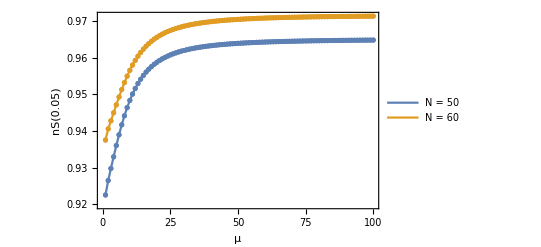

```mathematica
plot4 = ListPlot[{muns005n50,muns005n60},Joined->True,PlotRange->All,Mesh->Full,PlotLegends->Placed[{"N = 50","N = 60"},{Scaled[{0.5,0.3}], {0, 0.5}}],Frame->True,FrameLabel->{"μ","nS(0.05)"}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Presentation_plots\\mu_vs_ns005.png",plot4]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Presentation_plots\mu_vs_ns005.png

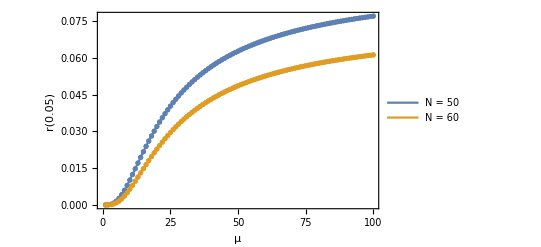

```mathematica
plot5 = ListPlot[{mur005n50,mur005n60},Joined->True,PlotRange->All,Mesh->Full,PlotLegends->Placed[{"N = 50","N = 60"},{Scaled[{0.5,0.3}], {0, 0.5}}],Frame->True,FrameLabel->{"μ","r(0.05)"}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Presentation_plots\\mu_vs_r005.png",plot5]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Presentation_plots\mu_vs_r005.png

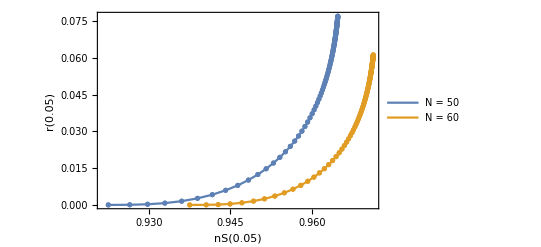

```mathematica
plot6 = ListPlot[{nsr005n50,nsr005n60},Joined->True,PlotRange->All,Mesh->Full,PlotLegends->Placed[{"N = 50","N = 60"},{Scaled[{0.2,0.3}], {0, 0.5}}],Frame->True,FrameLabel->{"nS(0.05)","r(0.05)"}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Presentation_plots\\ns_vs_r005.png",plot6]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Presentation_plots\ns_vs_r005.png